```mathematica
(* Hamilton & May dispersal model *)
```

```mathematica
(* Define expected fitness (sites occupied) by an invading mutant with dispersal rate v+d *)
```

```mathematica
EM=((v+d)p)/(1-v+v p)+(1-v-d)/(1-v-d+v p);
```

```mathematica
(* can manipulate expression to expand out and see the d^2 terms *)
```

```mathematica
Together[EM]
```

(1-d+d p-d^2 p-2 v+d v+2 p v-3 d p v+d p^2 v+v^2-2 p v^2+p^2 v^2)/((1-v+p v) (1-d-v+p v))

```mathematica
(* now set all terms containing d^2 to zero: *)
```

```mathematica
(1-d+d p-d^2 p-2 v+d v+2 p v-3 d p v+d p^2 v+v^2-2 p v^2+p^2 v^2)/((1-v+p v) (1-d-v+p v))/.d^2->0
```

(1-d+d p-2 v+d v+2 p v-3 d p v+d p^2 v+v^2-2 p v^2+p^2 v^2)/((1-v+p v) (1-d-v+p v))

```mathematica
(* solve for value of v that is resists invasion: *)
```

```mathematica
Solve[(1-d+d p-2 v+d v+2 p v-3 d p v+d p^2 v+v^2-2 p v^2+p^2 v^2)/((1-v+p v) (1-d-v+p v))==1,v]
```

{{v→1/(2-p)}}

```mathematica
(* plot invader fitness (blue) against common-type fitness (yellow) *)
```

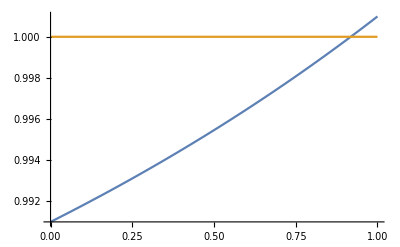

```mathematica
Plot[{EM/.{p->0.9,d->-0.01},1},{v,0,1}]
```

```mathematica
1/(2-p)/.p->0.9
```

0.909091

```mathematica
(* can also solve for ESS by taking derivative of invader fitness and finding value that of v that makes it zero *)
```

```mathematica
dEM=D[EM,d]/.d->0
```

(1-v)/(1-v+p v)^2-1/(1-v+p v)+p/(1-v+p v)

```mathematica
Solve[dEM==0,v]
```

{{v→1/(2-p)}}